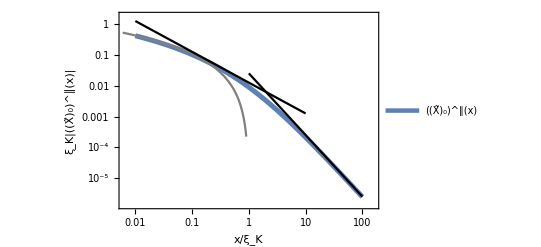

```mathematica
(*Universal scailing function for analytical non-magnetic case, x and y-axis rescaled and asymptotic behaviour shown *)
approxcor[x_]:=Abs[Exp[x]Gamma[0,x]/(2π)]^2
p1=LogLogPlot[{approxcor[x]},{x,0.01,100},PlotStyle->{Darker[0.5,Black],Thickness[0.009]},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/ξ_K","ξ_K|((X̃)_0)^∥(x)|"},PlotLegends->Placed[{"((X̃)_0)^∥(x)"},{Right,Top}]];
p2=LogLogPlot[Log[x]^2/(5 π^2),{x,0.006,1},PlotLegends->Placed[{"∼Log(x)^2"},{Left,Bottom}],PlotStyle->{Gray}];
p3=LogLogPlot[1/(8 π^2 x),{x,0.01,10},PlotLegends->Placed[{"∼1/x"},{Left,Bottom}],PlotStyle->{Black}];
p4=LogLogPlot[1/(4 π^2 x^2),{x,1,100},PlotLegends->Placed[{"∼1/x^2"},{Left,Bottom}],PlotStyle->{Black}];
Show[p1,p2,p3,p4]
```

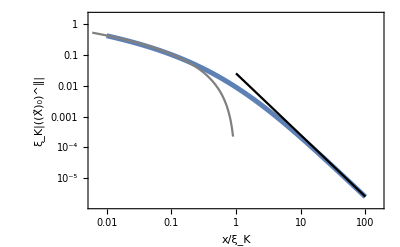

```mathematica
approxcor[x_]:=Abs[Exp[x]Gamma[0,x]/(2π)]^2
p1=LogLogPlot[{approxcor[x]},{x,0.01,100},PlotStyle->{Darker[0.5,Black],Thickness[0.009]},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/ξ_K","ξ_K|((X̃)_0)^∥|"}];
p2=LogLogPlot[Log[x]^2/(5 π^2),{x,0.006,1},PlotStyle->{Gray}];
p4=LogLogPlot[1/(4 π^2 x^2),{x,1,100},PlotStyle->{Black}];
Show[p1,p2,p4]
```